```mathematica
(*Final*)
```

```mathematica
(*----------------------------------------------------------------*)
(*---- Prepare global list for stroing vars and properties -----*)
(*----------------------------------------------------------------*)

(* ---------------- vars ----------------*)
nVars=0;(*Total number of variables*)
qs={};(*list vars: $q1[t],$q2[t],...,*)
qsvars={};(*List vars: $q1,$q2,...,*)
qsInit={};(*List initial value of qs*)
dqsInit={};(*List initial value of dqs*)
(* ------------ objects ----------------- *)
nObjects=0;
objNames={};
(*List: properties *)
masses={};
inertias={};
lens={};
g=5;
(*List: transformation matrices*)
Ts={};
(*List: front vertex of the link. Saved but not used.*)
pFronts={};
pBacks={};

(* ------------ impact ----------------- *)
(*List: vertices for impact detection *)
impObjVertexs={};
impObjVertexGroupIDs={};
(*List: edges for impact detection *)
impObjEdges={};
impObjEdgeGroupIDs={};

(* ------------ Funcs for creating objects ----------------- *)
IdxT=1;
IdxPFront=2;
IdxPBack=3;
IdxTFront=4;
IdxTBack=5;

(* Funcs for creating objects *)
createLink3DOFpp[p1_,p2_]:=Module[{l,T,pFront,pBack},
nObjects=nObjects+1;
{{p1x,p1y},{p2x,p2y}}={p1,p2};
l=CalcDist[p1x,p1y,p2x,p2y];
pushLensMassInertia[l];

(*Vars*)
nDOF=3;
{objqs,objqsvars}=pushVars[nDOF];
xvar=objqs[[1]];
yvar=objqs[[2]];
θvar=objqs[[3]];
{T,pFront,pBack,TFront,TBack}=calcAndPushT[xvar,yvar,θvar,l];

objqsinit={(p1x+p2x)/2,(p1y+p2y)/2,myArcTan[p1x,p1y,p2x,p2y]};
qsInit=Join[qsInit,objqsinit];
dqsInit=Join[dqsInit,Table[RandomReal[]*initRandVelocity,{i,1,nDOF}]];

(*Push vertices and edge for impact*)
pushVertex[pFront,nthGroup];
pushVertex[pBack,nthGroup];
pushEdge[pFront,pBack,nthGroup];

{T,pFront,pBack,TFront,TBack}(*Return*)
];

createLink1DOFgθl[T0_,θ0_,l_]:=Module[{T,pFront,pBack,x,y},
nObjects=nObjects+1;
pushLensMassInertia[l];

(*Vars*)
nDOF=1;
{objqs,objqsvars}=pushVars[nDOF];
θvar=objqs[[1]];

T=FullSimplify[T0.Rotz4[θvar].Trans4[l/2,0],qs∈Reals];
{pFront,pBack,TFront,TBack}=pushPEnds[T,l];
pushT[T];

qsInit=Append[qsInit,θ0];
dqsInit=Append[dqsInit,RandomReal[]*initRandVelocity];

(*Impact*)
pushVertex[pFront,nthGroup];
pushEdge[pFront,pBack,nthGroup];
{T,pFront,pBack,TFront,TBack}(*Return*)
];

createLink0DOFgθl[T0_,θ_,l_]:=Module[{T},
nObjects=nObjects+1;
pushLensMassInertia[l];

T=FullSimplify[T0.Rotz4[θ].Trans4[l/2,0],qs∈Reals];
{pFront,pBack,TFront,TBack}=pushPEnds[T,l];
pushT[T];

(*Impact*)
pushVertex[pFront,nthGroup];
pushEdge[pFront,pBack,nthGroup];
{T,pFront,pBack,TFront,TBack}(*Return*)
];

createLink0DOFpp[p1_,p2_]:=Module[{l,T,pFront,pBack},
nObjects=nObjects+1;
{{p1x,p1y},{p2x,p2y}}={p1,p2};
l=CalcDist[p1x,p1y,p2x,p2y];
pushLensMassInertia[l];

x=(p1x+p2x)/2;
y=(p1y+p2y)/2;
θ=myArcTan[p1x,p1y,p2x,p2y];

{T,pFront,pBack,TFront,TBack}=calcAndPushT[x,y,θ,l];

pushVertex[pFront,nthGroup];
pushVertex[pBack,nthGroup];
pushEdge[p1,p2,nthGroup];
{T,pFront,pBack,TFront,TBack}(*Return*)
];

(* ------------------------------------------------------------------------;-------------------------- Create objects here ---------------------------;---------------------------------------------------------------- *)
CreateObjects[];
```

```mathematica
(* Remove duplicated vertices by both symbolically and numerically check if two vertices are the same*)
n=Length[impObjVertexs];
tmpimpObjVertexs={};
tmpimpObjVertexGroupIDs={};
NumericalError=0.00001;
For[i=1,i≤n,i=i+1,
ifDup=False;
x0=impObjVertexs[[i,1]];
y0=impObjVertexs[[i,2]];
For[j=1,j≤Length[tmpimpObjVertexs],j=j+1,
If[ifDup==True,Break[]];
For[ktest=1,ktest≤5,ktest=ktest+1,(*Random some values to test, and check if two vertices are the same*)
tmpRep=Table[qs[[i]]->RandomReal[]*10000+10000,{i,1,nVars}];
errx=Abs[tmpimpObjVertexs[[j,1]]-x0]/.tmpRep;
erry=Abs[tmpimpObjVertexs[[j,2]]-y0]/.tmpRep;
(*Print[i," ",j," ",errx," ",erry," "];*)
If[errx<NumericalError &&erry<NumericalError,
ifDup=True;
Break[]
];
]];
If[ifDup==False,
AppendTo[tmpimpObjVertexs,impObjVertexs[[i]]];
AppendTo[tmpimpObjVertexGroupIDs,impObjVertexGroupIDs[[i]]]
];
];
impObjVertexs=tmpimpObjVertexs;
impObjVertexGroupIDs=tmpimpObjVertexGroupIDs;
```

```mathematica
(* Prepare *)
dqs=D[qs,t];
ddqs=D[dqs,t];
```

```mathematica
(* --------------- Left side of EL eqs -------------- *)
(*Kinetic energy*)
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
(*Potential energy*)
GetPE[m_,T_]:=m*g*T[[2,4]];
(* Body generalized mass, composed of Inertia Tensor and Mass Matrix *)
getGb[j_,m_]:=ArrayFlatten[({{DiagonalMatrix[{j,j,j}], Zeros[3,3]}, {Zeros[3,3], DiagonalMatrix[{m,m,m}]}})]
Gbs=Table[getGb[inertias[[i]],masses[[i]]],{i,1,nObjects}]//Simplify;
(* Body screw axis *)
Vbs=Table[GenUnhat[InvT[Ts[[i]]].D[Ts[[i]],t]],{i,1,nObjects}]//Simplify;
(* Lagrange Equations: Kinetic and Potential Energy *)
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
GetPE[m_,T_]:=m*g*T[[2,4]];
KEs=Table[GetKE[Gbs[[i]],Vbs[[i]]],{i,1,nObjects}]//Simplify;
PEs=Table[GetPE[masses[[i]],Ts[[i]]],{i,1,nObjects}]//Simplify;
Lag=Simplify[Total[Join[KEs,-PEs]],qs∈Reals];
(* Left side of Euler-Lagrange Equations*)
ELeqsLeft=Simplify[D[D[Lag,{dqs}],t]-D[Lag,{qs}],qs∈Reals];
```

```mathematica
(* --------------- Right side of EL eqs -------------- *)
(* Constraints *)
(*
conslink1P1x=p1Ends[[1]][[2,1]];(* y=0 *)
conslink1P1y=p1Ends[[2]][[2,1]];(* y=0 *)
*)
cons=Simplify[cons,qs∈Reals];
nCons=Length[cons];
If[nCons>0,
(λs=Transpose[{Table[Symbol["$λ"<>ToString@i],{i,nCons}]}];
consgrad=Transpose[Grad[cons,qs]]; (* Grad[2,5]->Mat(2,5),Transpose->(5,2)*)
consddt=Simplify[D[D[cons,t],t],qs∈Reals];)];
```

```mathematica
(* External forces *)
externalForces=ConstantArray[0,nVars];
```

```mathematica
(* ----------------------------- *)
(* Solve *)
If[nCons>0,(* with constraints *)
(EulerLagEqs=Thread[ELeqsLeft==Flatten[consgrad.λs]+externalForces]//Simplify;
consddtEqs=TurnToEq[consddt,ConstantArray[0,nCons]];
EQ=Solve[Join[EulerLagEqs,consddtEqs],Join[ddqs,Flatten[λs]]]),
(* No constraint *)
EulerLagEqs=Simplify[TurnToEq[ELeqsLeft,externalForces],qs∈Reals];
EQ=Solve[EulerLagEqs,ddqs]];
```

```mathematica
(* ----------------------------- *)
(* Preprae for NDSolve *)
timeend=10;
MAXIMPACTTIMES=100;
impactDetectionError=0.1;
intergrationMaxStepSize=0.01;
ifprint=False;

SetUpImpacts[];
ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];
```

```mathematica
(* NDsolve *)
{end,data,bounces}=BouncingBall[qsInit,dqsInit];
```

Computing simulation: 2.07609 / 10 ...

Computing simulation: 4.53424 / 10 ...

Computing simulation: 6.12442 / 10 ...

Computing simulation: 8.04913 / 10 ...

Computing simulation is completed.

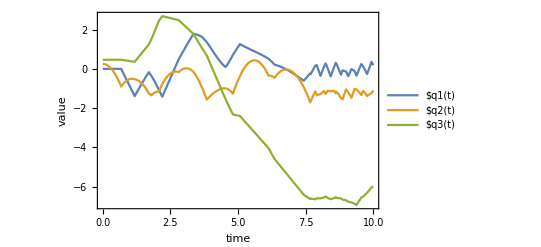

```mathematica
plotVariablesValues
```

```mathematica
plotAnimation
```